Created 2025.
Last edited March 2026.
 Email mustafa.a.amin@rice.edu if you have questions or corrections.
 
Please cite the following depending on your usage:
For particle-like DM with Warmth and Poisson :
- single species  Amin, Delos & Mirbabayi (2025)[https://arxiv.org/abs/2503.20881]. Also includes N-body simulations.
- multi-species, Amin, Delos & Yang (2025) [https://arxiv.org/abs/2510.15046]. Also includes (limited) N-body simulations.
For Wave DM with Warmth and Poisson:
- single species,  Amin, May & Mirbabayi (2025) [https://arxiv.org/abs/2506.12131]. Includes nonlinear Schrodinger-Poisson simulations.
- multi-species,   Amin & Delos (2025) [https://arxiv.org/abs/2510.17977]. Most general, can include the particle case also.

Earlier papers (which did not rely on numerical evaluation of the power spectra) include Amin & Mirbabayi (2022) [https://arxiv.org/abs/2211.09775] and Ling and Amin (2023) [https://arxiv.org/abs/2408.05591] (simulations in the early universe).

# Volterra Solvers and Power Spectra for Multi-Species Wave Dark Matter

## Parameters

```mathematica
Quit[];
```

```mathematica
(*----Cosmological constants----------------------------------------*)
Mpc=1.;                        (*all k in units of Mpc^-1*)
eV=1.56 10^29 Mpc^-1;        (*unit conversion*)
keq=0.01 Mpc^-1;              (*comoving wavenumber at equality*)
aeq=1/3388.;                   (*scale factor at equality*)

(*~~~~~~~ Numerical Resolution ~~~~~~~*)
{y0,yf}={10^-3.,10^3.};          (*y = a/Subscript[a, eq] range*)
{kmin,kmax}={0.5,9*10^3};           (*k range in [Mpc^-1]*)
{Ny,Nit,Nk}={600,15,60};          (*y-pts, Picard iterations ,k-pts*)
yout={0.01,0.1,1.,10.,100.,1000.}; (*output y values*)

(*~~~~~~~ Model Cases ~~~~~~~*)
(*Each entry:list of {fraction Subscript[f, s], mass Subscript[m, s], momentum k_(* s)} with Subscript[Σ, s] Subscript[f, s]=1*)
(*Subscript[f^s, 0](p)=(2π)^(3/2) k*s^-3 exp(-p^2/2 k*s^2)*)
(*k*_s->0:globally misaligned (cold wave)-- fuzzy DM limit*)
(*k*_s-> ∞ :particle limit (cold or warm depending on k*_s/m_s)*)
(* You can build you own cases, possible to include more than 2 species also *)
cases=<|
"CDM"->{{1.0,10^-5. eV,10^9. Mpc^-1} ,{0.0,10^-5. eV,10^9. Mpc^-1} (* this is effectively CDM, only one component active*)},"CDM + warm wave"->{(*Fig.3 of paper*){0.9,10^-5.  eV,10^9.  Mpc^-1}(*effectively CDM*),{0.1,10^-19. eV,10^3.  Mpc^-1}    (*warm wave,locally mis.*)},"cold wave + warm wave"->{(*Fig.1 of paper*){0.9,10^-19. eV,10^-13. Mpc^-1}(*globally misaligned*),{0.1,10^-19. eV,10^3.   Mpc^-1}   (*warm wave*)}
|>;
(* this say which case to evaluate*)
Model=cases["CDM + warm wave"];  
CDM=cases["CDM"];
```

## The Main Computation

```mathematica
(*~~~~~ k-independent grid ~~~~*)
(*Log-spaced y-grid and geometric midpoints m_i=sqrt(y_i*y_{i+1})*)
ygrid=Exp@Subdivide[Log[y0],Log[yf],Ny-1];
midpts=Sqrt[Most[ygrid]*Rest[ygrid]];
Nmid=Length[midpts];

(*Step-size factor:y_{i+1}-y_i=y_i*r  (exact for log spacing)*)
r=Sqrt[ygrid[[2]]/ygrid[[1]]]-Sqrt[ygrid[[1]]/ygrid[[2]]];

(*Log-spaced k-grid*)
klist=Exp@Subdivide[Log[kmin],Log[kmax],Nk-1];

(*k-independent matrices (computed once,reused for every k)*)
(*F[[i,j]]=F(m_i,m_j) -- comoving distance function *)
F=Outer[Log[#1/#2 (1+√(1+#2))^2/(1+√(1+#1))^2]&,midpts,midpts]; (* distance function as a matrix of y and y'*)
(*DY[[i,j]]=dy'/√(1+y') evaluated at y'=m_j:integration measure *)
DY=Outer[(#2 r)/Sqrt[1+#2]&,midpts,midpts]; (* integration measure as a vector *)
(*Causal mask:enforce y>y' (lower triangular,diagonal excluded)*)
mask=LowerTriangularize[ConstantArray[1.,{Nmid,Nmid}],-1]; (* y>y' *)

(*~~~~~ main module ~~~~~~*)
ClearAll[computeT,Piso]
(*Piso[sp,k]:initial isocurvature power spectrum. For Gaussian Subscript[f^s, 0](p), we have Subscript[P, iso] for each species being Subscript[f, s]^2 π^(3/2)/Subscript[k, s]^3 ⅇ^(-k^2/(4 Subscript[k, s]^2))*)
Piso[sp_,k_]:=Total[(π^(3/2)(#[[1]])^2)/(#[[3]])^3 ⅇ^(-k^2/(4(#[[3]])^2))  &/@sp]
(*computeT[sp,k,Nit,F,DY,mask]. Solves the Volterra equations (2.12) for T^(a,b,c)_k by Picard. Iteration returns {k,Ta,Tb,Tc}.*)(*Picard iteration step:T^(i)<-Tfs^(i)+KK.T^(i)   (i=a,b,c)*)
computeT[sp_,k_,Nit_,F_,DY_,mask_]:=Module[{piso,Tfsa,Tfsb,Tfsc,KK,Ta,Tb,Tc},
(*~~~~~~~~~Free-streaming Kernels ~~~~~~~~*)
piso=Piso[sp,k];
(* These a are density fraction Subscript[f, i] weighted sums of single species kernels *)
(* Note that #[[1]]->Subscript[f, s], #[[2]]-> Subscript[m, s] and #[[3]]->Subscript[k, s] *)
Tfsa=Total[(#[[1]]Cos[k^2/(√2 aeq keq #[[2]])F]Exp[-(k/keq)^2((#[[3]])/(aeq #[[2]]))^2 F^2])&/@sp]*mask;
Tfsb=Total[F*(#[[1]] Sinc[k^2/(√2 aeq keq #[[2]])F]Exp[-(k/keq)^2((#[[3]])/(aeq #[[2]]))^2 F^2])&/@sp]*mask;
Tfsc=Total[(((π^(3/2)(#[[1]])^2)/(#[[3]])^3 ⅇ^(-k^2/(4(#[[3]])^2))Exp[-1/2(k/keq)^2((#[[3]])/(aeq #[[2]]))^2 F^2])/piso//Quiet)&/@sp]*mask;
(*~~~~~~~~~Kernel of Volterra Eq. ~~~~~~~~*)
KK=3/2*DY*Tfsb;
(*~~~~~~~~~Initialize~~~~~~~~*)
Tb=Tfsb;
Ta=Tfsa;
Tc=Tfsc;
(*~~~~~~~~Iterate~~~~~~~~*)
Do[
Tb=Tfsb+KK.Tb;
Ta=Tfsa+KK.Ta;
Tc=Tfsc+KK.Tc;,{Nit}];
{k,Ta,Tb,Tc}]

(*~~~~~~~ execute ~~~~~~~*)

(*---- This is the actual evalation  ------------------------------------*)
{time,resultsModel}=AbsoluteTiming[ParallelTable[computeT[Model,k,Nit,F,DY,mask],{k,klist}]];
Print[Length[klist]," k values in ",time," s"]
```

60 k values in 6.72095 s

```mathematica
(*---- You can also evaluate CDM case for comparison, otherwise leave it alone ------------------------------------*)
{time,resultsCDM}=AbsoluteTiming[ParallelTable[computeT[CDM,k,Nit,F,DY,mask],{k,klist}]];
Print["For CDM ",Length[klist]," k values in ",time," s"]
```

For CDM60 k values in 6.74503 s

## Power Spectrum Assembly

```mathematica
(*~~~~~~~ Power Spectra Assembly ~~~~~~~*)
(*Integration weight dy/√(1+y) evaluated at midpoints*)
dy=(r*midpts)/(√(1+midpts));
(*k-list extracted from results (same for CDM and model of interest)*)
kk=resultsModel[[All,1]];

(* The primordial curvature spectrum k^3/(2 π^2)Subscript[P, R](Subscript[y, 0],k) and its log derivative evaluated on subhorizon scales at Subscript[y, 0] *)
PR[j_]:=2 10^-9(36(3+Log[0.15 kk[[j]]/keq]-Log[4/y0])^2);
dlnPdlny[j_]:=2/(3+Log[0.15 klist[[j]]/keq]-Log[4/y0]);

(* Assemble PS at a given output time Y from a results array. Returns {y,Piso(y,k),Pad(y,k)}*)
assemblePS[sp_,res_,Y_]:=Module[{i0,PSiso,PSad},i0=Nearest[midpts->"Index",Y][[1]];
(*Isocurvature:k^3/(2 π^2)P^(iso)(Subscript[y, 0],k)(1+3 ∫dy'/sqrt(1+y') Tb(y,y') Tc(y,y'))*)PSiso=Table[With[{Tb=res[[j,3]],Tc=res[[j,4]]},kk[[j]]^3/(2 π^2)Piso[sp,klist[[j]]]*(1+3 (dy[[1;;i0-1]].(Tc[[i0,1;;i0-1]]*Tb[[i0,1;;i0-1]])))],{j,Length[res]}];
(*(P^(ad)(y,k)=k^3/(2 π^2)Subscript[P, R](Subscript[y, 0],k)(Ta(y,Subscript[y, 0])+1/2 √(1+Subscript[y, 0])] (d ln P)/(d ln y)(Subscript[y, 0],k)*Tb(y,y0)]))^2*)PSad=Table[With[{Ta=res[[j,2]],Tb=res[[j,3]]},PR[j]*(Ta[[i0,1]]+1/2 √(1+y0) dlnPdlny[j]*Tb[[i0,1]])^2],{j,Length[res]}];
{midpts[[i0]],PSiso,PSad}]
```

## Power Spectrum Plotting (evaluate before plotting)

```mathematica
(*~~~~~~~ Plot Variables (aesthetics) ~~~~~~~*)

nn=Length[yout];
(*Tick marks*)
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
labeledTicks2=Table[{10^(2i),Superscript[10,2i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
xmyTicks=Join[labeledTicks,unlabeledTicks];
ymyTicks=Join[labeledTicks,unlabeledTicks];
ymyTicks2=Join[labeledTicks2,unlabeledTicks];
NullmyTicks=unlabeledTicks;
MyTicks={{ymyTicks2,NullmyTicks},{xmyTicks,NullmyTicks}};
(*Coolwarm colormap (blue->white->red)*)
coolwarm=Blend[{RGBColor[59/255,76/255,192/255],RGBColor[98/255,130/255,234/255],RGBColor[141/255,176/255,254/255],RGBColor[185/255,210/255,237/255],RGBColor[221/255,221/255,221/255],RGBColor[245/255,196/255,173/255],RGBColor[244/255,152/255,120/255],RGBColor[221/255,96/255,78/255],RGBColor[180/255,4/255,38/255]},#]&;

styles=Directive[Thick,#]&/@(coolwarm/@Subdivide[0,1,nn-1]);
stylesCDM=Directive[{Thick,Opacity[0.25]},#]&/@(coolwarm/@Subdivide[0,1,nn-1]);

legend=LineLegend[styles,Row[{Superscript[10,Round[Log10[#]]]}]&/@yout,LegendLayout->{"Column",0.1},LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->14},LegendLabel->"y = a/a_eq"];
```

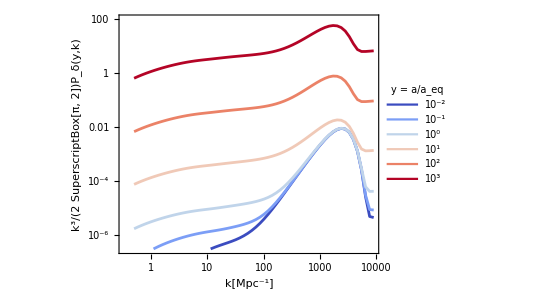

```mathematica
(*~~~~~~~ Power Spectra Plotting ~~~~~~~*)

(* species was stated at the beginning of notebook *)
modelSpectra=assemblePS[Model,resultsModel,#]&/@yout;

plotData=Table[Transpose[{kk,modelSpectra[[j,2]] (* isocurvature *)+modelSpectra[[j,3]] (* adiabatic *)}],{j,Length[yout]}];

plotTot=ListLogLogPlot[plotData,PlotLegends->Placed[legend,Right],Frame->True,FrameLabel->{{"k^3/(2 SuperscriptBox[π, 2])P_δ(y,k)"," "},{"k[Mpc^-1]"," "}},Joined->True,PlotMarkers->None,PlotStyle->styles,BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->16},ImageSize->400,AspectRatio->3/4,PlotRange->{All,{10^-6.5,99.}},FrameTicks->MyTicks]
```

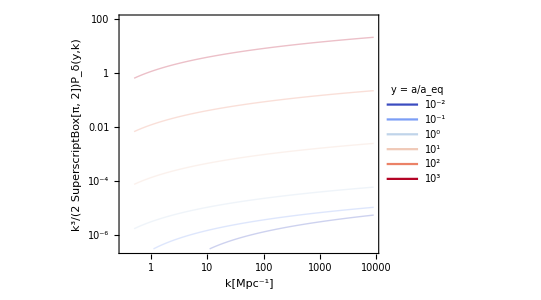

```mathematica
(*~~~~~~~ Power Spectra Plotting for CDM ~~~~~~~*)

(* species was stated at the beginning of notebook *)
CDMSpectra=assemblePS[CDM,resultsCDM,#]&/@yout;

plotDataCDM=Table[Transpose[{kk,CDMSpectra[[j,2]] (* isocurvature *)+CDMSpectra[[j,3]] (* adiabatic *)}],{j,Length[yout]}];

plotTotCDM=ListLogLogPlot[plotDataCDM,PlotLegends->Placed[legend,Right],Frame->True,FrameLabel->{{"k^3/(2 SuperscriptBox[π, 2])P_δ(y,k)"," "},{"k[Mpc^-1]"," "}},Joined->True,PlotMarkers->None,PlotStyle->stylesCDM,BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->16},ImageSize->400,AspectRatio->3/4,PlotRange->{All,{10^-6.5,99.}},FrameTicks->MyTicks]
```